```mathematica
Normalize[{2,2}]
```

{1/(√2),1/(√2)}

```mathematica
ccw90[p_]:={p[[2]],-p[[1]]}
cw90[p_]:={-p[[2]],p[[1]]}
```

```mathematica
capsule[a_,b_,r_]:=(
 diff=b-a;
 u=Normalize[ccw90[diff]]*r;
d=Normalize[cw90[diff]]*r;
aUp=a+u;
aDown=a+d;
bUp=b+u;
bDown=b+d;
{Circle[a,r],Line[{aUp,bUp}],Line[{aDown,bDown}],Circle[b,r]}
)
upside[a_,b_,r_]:=(
diff=b-a;
 u=Normalize[ccw90[diff]]*r;
d=Normalize[cw90[diff]]*r;
aUp=a+u;
aDown=a+d;
bUp=b+u;
bDown=b+d;
Line[{aUp,bUp}]
)
```

```mathematica
stroke17={6.875,6.375};
stroke18={7.21875,7.0};
stroke20={7.96875,7.9375};
stroke21={8.34375,8.1875};
```

enters at 17.48290604935480397
exits at 17.0.9075077419106311
exits at 20.7889052396611623

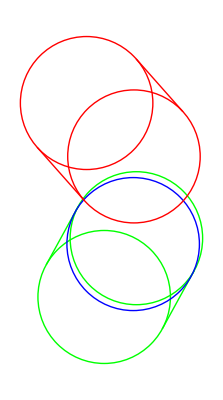

```mathematica
Graphics[{Green,capsule[stroke17,stroke18,Sqrt[0.5]],Blue,Circle[stroke17+.90(stroke18-stroke17),Sqrt[0.5]],Red,capsule[{6.6875,8.4375},{7.1875,7.875},Sqrt[0.5]]}]
```

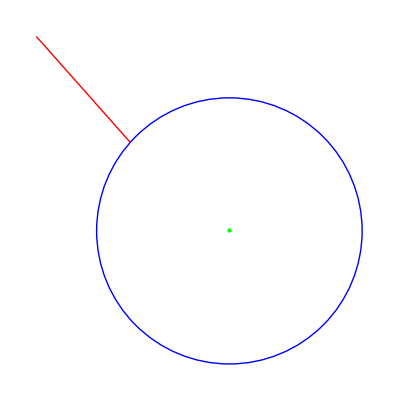

```mathematica
Graphics[{Green,Point[{7.1869557862817794,6.942192338694144}],Blue,Circle[stroke17+.90(stroke18-stroke17),Sqrt[0.5]],Red,upside[{6.6875,8.4375},{7.1875,7.875},Sqrt[0.5]]}]
```

{6.3138,8.10532}

{6.8138,7.54282}

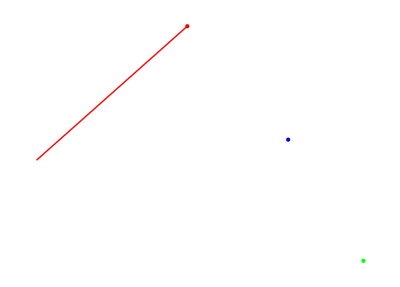

```mathematica
a={6.31379534065817,8.10531808058504}
b={6.81379534065817,7.54281808058504}
p={7.1869557862817794,6.942192338694144};
 diff=b-a;
norm=Normalize[ccw90[diff]];
Graphics[{Red,Point[a],Blue,Point[b],Red,Line[{a,a+norm}],Green,Point[p]}]
```

```mathematica
pDistance=Dot[p-a,norm]
```

0.12013

outside = true
topside:
0.9075077419106311
bcap:
0.48290604935480397

```mathematica
1.5-1.4986422195363014
```

0.00135778

```mathematica
0.0013577804636986102/5.0
```

0.000271556

```mathematica
param=0.00027155609273972204
```

0.000271556

```mathematica
0.004661554773294973*5
```

0.0233078